```mathematica
(* my Mathematica utilities *)<<"https://raw.githubusercontent.com/Andrew-Schwartz/YouTilities/master/YouTilities.m"
```

### 1. Model Selection for Bayesians: the Bayes Factor

In Bayesian model selection, the probability of a model  given data  is

 

where 

  oh no no amsmath=no integral sign 

and the vector  represents the parameters of model . In the likelihood  we marginalize over the prior distributions of the model parameters. The “evidence”  is calculated by summing over all models of interest. When choosing between two models  and , we calculate the posterior odds 



Assuming no reason to favor model  over  before taking data, the posterior odds ratio reduces to the Bayes factor . Calculating  is not necessary.

```mathematica
dataString="0.02    -0.26     0.10 
    0.03    -0.25     0.10 
    0.05    -0.09     0.10 
    0.13    -0.18     0.10 
    0.21    -0.06     0.10 
    0.26    -0.03     0.10 
    0.28     0.28     0.10 
    0.29    -0.03     0.10 
    0.42     0.11     0.10 
    0.44     0.22     0.10 
    0.46     0.23     0.10 
    0.51     0.29     0.10 
    0.55     0.45     0.10 
    0.56     0.12     0.10 
    0.59     0.33     0.10 
    0.65     0.52     0.10 
    0.68     0.35     0.10 
    0.71     0.40     0.10 
    0.89     0.84     0.10 
    0.90     0.72     0.10";
```

#### (a)

Consider  the    data  plotted  below, which  you  can  access  in  the  file  model     on  Blackboard. 

Let    correspond  to  a  linear  model  with  two  parameters   , 

 

Assuming  flat  priors  on    and  , calculate    if  the  uncertainties  on  the  data  are Gaussian . When  (numerically)  integrating  the  likelihood, you  can  assume  that  the  range  of    and    is  between - 2  and  2.

```mathematica
(* Import data as columns of x, y, dy data and Rationalize it to make it exact fractions rather than approximate floating point numbers *){x,y,dy}=ImportString[dataString,"Table"]ᵀ//Rationalize;(* all dy are the same so no need to keep them all *)
dy=dy[[1]];
(* number of data points *)n=Length@x;
```

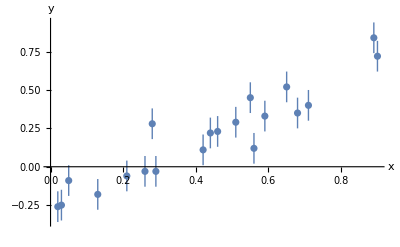

```mathematica
(* we'll use this bad boy later *)
errPlot=ListPlot[{x,Around[#,dy]&/@y}ᵀ, AxesLabel->{"x","y"}]
```

```mathematica
dy^2
```

1/100

```mathematica
(* Likelihood function *)
p["D|",a_,b_]:=(1/(2π dy^2))^(n/2)Exp[-((y-(a+b x)).(y-(a+b x)))/(2 dy^2)]
```

```mathematica
p["D|",-0.26,1.06]
```

3.02555×10^7

```mathematica
N[(1/(2π dy^2))^(n/2),50]
```

1.0428007057481966466836700734328536540951994235163×10^12

```mathematica
(* prior in any number of variables from -2 to 2*)
(*ClearAll[p]*)
p[a__,"|M"]:=(1/4)^(Length@{a})
```

```mathematica
∫_-2^2 ∫_-2^2 p["D|",a,b]p[a,b,"|M"]ⅆaⅆb
```

∫_-2^2 (30517578125000 √10 ⅇ^((-354104+(584664-273611 b) b)/4000) (Erf[(4396-863 b)/(20 √10)]+Erf[(3604+863 b)/(20 √10)]))/π^(19/2)ⅆb

```mathematica
p["D|M_1"]=%//N
```

22833.2

#### (b)

Let  correspond to a quadratic model with three parameters , 

 

Calculate , using the same priors on  and  and a uniform prior on  (which you may also assume has a range of -2 to 2).

```mathematica
(* Likelihood function *)
p["D|",a_,b_,c_]:=(1/(2π dy^2))^(n/2)Exp[-((y-(a+b x+c x^2)).(y-(a+b x+c x^2)))/(2 dy^2)]
```

```mathematica
∫_-2^2 ∫_-2^2 ∫_-2^2 p["D|",a,b,c]p[a,b,c,"|M"]ⅆaⅆbⅆc
```

1/π^(19/2)7629394531250 √10 ∫_-2^2 ∫_-2^2 ⅇ^((-10000 (354104+b (-584664+273611 b))+1400 (3741228-3416989 b) c-2291326059 c^2)/40000000) (-Erf[(-439600+86300 b+50919 c)/(2000 √10)]+Erf[(360400+86300 b+50919 c)/(2000 √10)])ⅆbⅆc

```mathematica
p["D|M_2"]=%//N
```

7454.56

### (c)

Compute the Bayes Factor B_12. Do you favor model M_1 or the more complex model M_2? Justify your answer.

```mathematica
Subscript[B, 12]=p["D|M_1"]/p["D|M_2"]
```

3.06298

I favor model , since the Bayes factor points to it being the better model and it has more predictive power as it is less likely to be overfitting.

### 2.

Repeat the model selection of the previous problem, but this time use a frequentist approach
on the data in  to determine if the linear or quadratic model is a better
fit.

#### (a)

Consider a model  in which the data are described by the linear relationship 
	
Minimize the chi-square test statistic for this linear model, where the test statistic is given by the sum of the square of the residuals
	.

Report  and the best estimates of  and . Plot the best fit line on top of the data.

Using the fact that  is asymptotically distributed like  (a chi-square with  degrees of freedom) calculate the -value that the data are a random fluctuation from the linear model.

```mathematica
(* helper function to make a Hessian matrix *)
hessian[f_,xs__]:=D[f[xs],{{xs},2}]
```

```mathematica
weight=2/dy^2;
(* same p and q as defined in class, and r is for the quadratic term *)
{p,q,r}=Total[weight y x^#]&/@{0,1,2};
```

```mathematica
χ2M1[a_,b_]:=∑_(i=1)^n ((y[[i]]-(a+b x[[i]]))/dy)^2;
```

```mathematica
Solve[hessian[χ2M1,a,b].{â,b̂}=={p,q},{â,b̂}][[1]]//N
{Subscript[â, 1],Subscript[b̂, 1]}={â,b̂}/.%;
χ2M1min=χ2M1@@{Subscript[â, 1],Subscript[b̂, 1]};
Print["χ_M_1^2 = ",χ2M1min]
```

{â→-0.263024,b̂→1.06842}

χ_M_1^2 = 20.885

```mathematica
p1=1-CDF[ChiSquareDistribution[n-2],χ2M1min];
Print["p-value = ",p1]
```

p-value = 0.285253

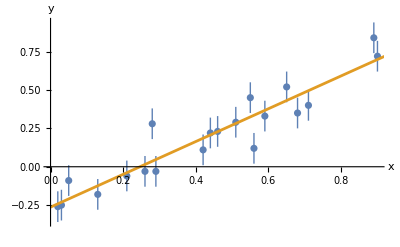

```mathematica
Show[
errPlot,
Plot[Subscript[â, 1]+Subscript[b̂, 1] x,{x,0,1},ColorFunction->(defaultColorData[][2]&)]
]
```

#### (b)

Repeat part (a) for the quadratic model , where  

I.e., minimize and report  and the best estimates , , and , and plot the best fit line on top of the data. 

Using the fact that  is asymptotically distributed like  – a chi-square with N-3 degrees of freedom – calculate the -value that the data are a random fluctuation from the quadratic model.

```mathematica
χ2M2[a_,b_,c_]:=∑_(i=1)^n ((y[[i]]-(a+b x[[i]]+c x[[i]]^2))/dy)^2;
```

```mathematica
Solve[hessian[χ2M2,a,b,c].{â,b̂,ĉ}=={p,q,r},{â,b̂,ĉ}][[1]]//N
{Subscript[â, 2],Subscript[b̂, 2],Subscript[ĉ, 2]}={â,b̂,ĉ}/.%;
χ2M2min=χ2M2@@{Subscript[â, 2],Subscript[b̂, 2],Subscript[ĉ, 2]};
Print["χ_M_2^2 = ",χ2M2min]
```

{â→-0.224276,b̂→0.792178,ĉ→0.315999}

χ_M_2^2 = 19.8848

```mathematica
p2=1-CDF[ChiSquareDistribution[n-3],χ2M2min];
Print["p-value = ",p2]
```

p-value = 0.280166

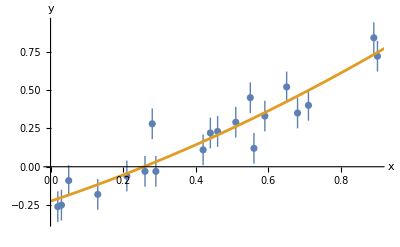

```mathematica
Show[
errPlot,
Plot[Subscript[â, 2]+Subscript[b̂, 2] x+Subscript[ĉ, 2] x^2,{x,0,1},ColorFunction->(defaultColorData[][2]&)]
]
```

#### (c)

Models  and  are nested: that is, the parameters of  are a subset of
. Therefore, the chi-square difference  should be distributed like . I.e., 



where the number of degrees of freedom is equal to the difference between the number of parameters in the two models (). This result is known as Wilks’ Theorem.

A large chi-square difference implies that the difference between the two models fits is
statistically significant. Calculate  for models  and  and compute its -value. Is the difference between the models statistically significant? Justify your answer given what you know about the pitfalls of model selection with -values.

```mathematica
Δχ2=χ2M1min-χ2M2min
```

1.00028

```mathematica
Δp=1-CDF[ChiSquareDistribution[1],Δχ2];
Print["p-value = ",Δp]
```

p-value = 0.317242

Since the p-value is above 0.05, the difference is not statistically significant. This supports our claim in 1c, where we continue to favor model  because it is simpler and is not statistically significantly worse.